# Mathematica Collagen Analysis

Numerical Constants

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

L = 5;
m = 20;

MAX=2m+1;

σ = 1;
κ  =1;
Δ = L/(2m)//N;
Print["\nDelta:",Δ,"\n"]

v[η_]:=(σ η^2)/κ

umin = 0;
uMAX=20;


M=Table[0,{i,1,MAX^2},{j,1,MAX^2}];
V[η_, ξ_] :=   v[(2 η)/(√κ)] + v[(η + √3 ξ)/(√κ)] + v[(√3 ξ - η)/(√κ)];
T̂[ η1_, η2_, ξ1_, ξ2_] :=   Exp[-(η1 - η2)^2] Exp[-(ξ1 - ξ2)^2] Exp[-V[η1, ξ1]/2] Exp[-V[η2, ξ2]/2];
OverHat[MT]=Table[ Δ^2 T̂[Δ η1, Δ η2,Δ ξ1, Δ ξ2], {η1, -m,m}, {η2,-m, m}, {ξ1,-m, m}, {ξ2,-m, m}] // N;

r[x_,y_]:=(x-1) MAX+y;
Do[
M[[r[k,i],r[j,l]]]=OverHat[MT][[k,j]][[i,l]],{k,1,MAX},{i,1,MAX},{j,1,MAX},{l,1,MAX}
]
M==Transpose[M];

β=4;
μ=(12 σ)/κ//N;
c=((μ^2+2 β μ)^(1/2))/2//N;
δ=2 c+μ+β;
b=1/2 ((δ^2-β^2)/δ)^(1/2)//N;
k=Log[δ/β]//N;
Subscript[e, 0]=((4 π)/δ)^(1/2)//N;
Subscript[E, 00][h_]:=Subscript[e, 0] Exp[-k h];
Subscript[C, 0]=1/2 ((2 π)/((μ^2+2 β μ)^(1/2)))^(-1/4);
gC[n_]:=(1/(2^n Factorial[n]))^(1/2);

OverHat[λA][n_]:=Subscript[e, 0] Exp[-k n];
OverHat[ψA][n_,η_]:=2 Subscript[C, 0] gC[n] HermiteH[n,b η] Exp[-(c η^2)/2];

OverHat[ψAij][n1_,n2_,η1_,η2_]:=OverHat[ψA][n1,η1]*OverHat[ψA][n2,η2];

FirstEvalλA=0;
LastEvalλA=10;

ψm=(MAX^2-1)/2;

λ=Take[Eigenvalues[M],30];
```

/homes/ht/Desktop/CORRECTIONSv1/Results/Collagen/Eigensystem/Hypermatrix/Eigenvalues

Delta:0.125

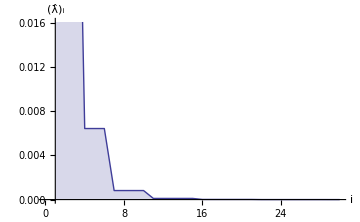
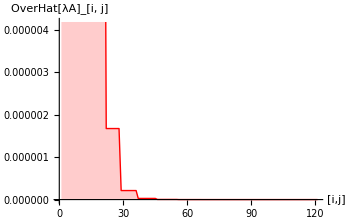

```mathematica
λp=ListLinePlot[λ,PlotStyle->{Thick},AxesOrigin->{1,0},AxesLabel->{Style["i",FontSize->18],Style["(λ̂)_i",FontSize->18]},Filling->Axis,PlotStyle->Thick,ImageSize->Medium];

dataλA=Sort[Flatten[Table[OverHat[λA][i]*OverHat[λA][j],{i,FirstEvalλA,LastEvalλA},{j,FirstEvalλA,LastEvalλA}]],Greater];
λAp1=ListLinePlot[dataλA,PlotStyle->{Red,Thick},Filling->Axis,FillingStyle->Lighter[Red,0.8],ImageSize->Medium,AxesLabel->{Style["[i,j]",FontSize->18],Style["OverHat[λA]_[i, j]",FontSize->18]}];

{λp,λAp1}
```

Eigenvalues Comparison Analysis

### λ̂

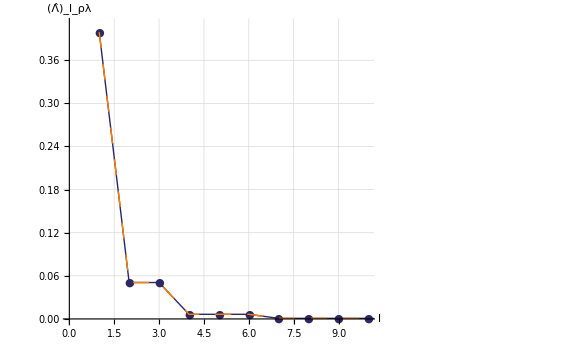

/homes/ht/Desktop/CORRECTIONSv1/Results/Collagen/Eigensystem/Hypermatrix/Eigenvalues/0.125

0.125/lambda_t_ij_L5_m20.pdf

0.125/3D_lambda_ij_L5_m20.pdf

```mathematica
fsAxesLabel=24;
fs2=18;

p1=ListLinePlot[λ,PlotStyle->{Thick,Darker[ColorData[1,1]]},PlotMarkers->{"●"},PlotRange->{{0,10},{0,0.41}}];
p2=ListLinePlot[dataλA,PlotStyle->{Thick,Dashing[0.02],Orange},PlotRange->{{0,10},{0,0.41}}];
{p1,p2};

legend={
{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],PointSize[Large],Point[{1,0}],Line[{{0,0},{2,0}}]}],Style["Numerical",FontSize->fs2]},
{Graphics[{Thick,Dashing[0.01],Orange,Line[{{0,0},{2,0}}]}],Style["Analytical",FontSize->fs2]}
};

EvalPlotλ=ShowLegend[
Show[
{p1,p2},
PlotRange->{{0,10},{0,0.41}},
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["l",FontSize->fsAxesLabel],
Style["(Λ̂)_l_ρλ",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
],
{
legend,
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->0.5,
LegendPosition->{0.1,0.1},
PlotRange->{{1,10},{0,0.42}}
}
]
λAp3d=Plot3D[OverHat[λA][i]OverHat[λA][j],{i,FirstEvalλA,LastEvalλA},{j,FirstEvalλA,LastEvalλA},PlotStyle->{Thick},Filling->Axis,AxesOrigin->{0,0},AxesLabel->{Style["  i  ",FontSize->fsAxesLabel],Style["  j  ",FontSize->fsAxesLabel],Style["  (λ̂)_ij  ",FontSize->fsAxesLabel]},PlotRange->{{0,2},{0,2},{0,0.45}},LabelStyle->{"Times",FontSize->fs2},PlotStyle->Thick,ImageSize->Large,PlotRange->All];

CreateDirectory[ToString[Δ]]
ExportFilename= ToString[Δ]<>"/lambda_t_ij_L"<>ToString[L]<>"_m"<>ToString[m]<>".pdf"
ExportFilename3D= ToString[Δ]<>"/3D_lambda_ij_L"<>ToString[L]<>"_m"<>ToString[m]<>".pdf"
```

```mathematica
Export[ExportFilename,EvalPlotλ]
(*Export[ExportFilename3D,Rasterize[λAp3d,ImageResolution->120]]*)
```

0.125/lambda_t_ij_L5_m20.pdf